## Inicializaciones

```mathematica
θA=π/2.;
```

```mathematica
θBplus=π/4.;
```

```mathematica
θBminus= -π/8.;
```

```mathematica
{a,b}={1.,0.};
```

```mathematica
psi0=ArrayPad[{a,b},2];
```

## Definiciones

### Funciones externas

```mathematica
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
```

### Operadores

#### Coin A

```mathematica
expCoinA={{Cos[θA/2.],-Sin[θA/2.]},{Sin[θA/2.],Cos[θA/2.]}};
```

```mathematica
CoinA[t_Integer]:=KroneckerProduct[SparseArray[Table[{i,i}->1.,{i,2 t+1}]],SparseArray[expCoinA]]
```

#### Coin B

```mathematica
θB[x_Integer]:=(θBplus(1.+Tanh[x])+θBminus(1.-Tanh[x]))/2
```

```mathematica
expCoinB[x_Integer]:={{Cos[θB[x]/2.],-Sin[θB[x]/2.]},{Sin[θB[x]/2.],Cos[θB[x]/2.]}}
```

```mathematica
CoinB[t_Integer]:=BlockDiagonalMatrix[expCoinB/@Range[-t,t],TargetStructure->"Sparse"]
```

#### Shift

```mathematica
Shift[t_Integer]:=SparseArray[Join[Table[{i,i+2},{i,Range[2,#-2,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1.,{#,#}]&[2*(2*t+1)]
```

#### Unitaria

```mathematica
Unitary[t_Integer,m_Integer,n_Integer]:=Shift[t].Dot@@Join[ConstantArray[CoinA[t],m],ConstantArray[CoinB[t],n]]
```

### Funciones cálculos

#### Caminata

```mathematica
DQWL[psi0_,t_Integer,m_Integer,n_Integer]:=
Module[{psi},
psi=ArrayPad[psi0,2];
Do[psi=ArrayPad[Chop[#.psi]&[Unitary[i,m,n]],2],{i,t}];
psi
]
```

```mathematica
PosProbDistrib[psi_,tmax_]:=Chop[Total[Abs[psi[[#;;#+1]]]^2]&/@Range[1,2*(2*tmax+3),2]]
```

```mathematica
PosProbDistribM[psi_,t_]:=Abs@Diagonal@MatrixPartialTrace[{psi}ᵀ.Conjugate[{psi}],1,{2t+3,2}]
```

```mathematica
psi0={a,b};t=1;m=1;n=0;
psi=DQWL[psi0,t,m,n]
PosProbDistribM[psi,t]
```

{0,0,0,0.707107,0,0,0.707107,0,0,0}

{0.5,0.5}

```mathematica
psi0={a,b};t=1;m=1;n=0;
psi=DQWL[psi0,t,m,n]
PosProbDistrib[psi,t]
```

{0,0,0,0.707107,0,0,0.707107,0,0,0}

{0,0.5,0,0.5,0}

```mathematica
psi0={a,b};t=0;m=1;n=0;
psi=DQWL[psi0,t,m,n]
PosProbDistribM[psi,t]
```

{0,0,1.,0.,0,0}

{1.,0.}

```mathematica
psi0={a,b};t=0;m=1;n=0;
psi=DQWL[psi0,t,m,n]
PosProbDistrib[psi,t]
```

{0,0,1.,0.,0,0}

{0,1.,0}

#### Con Table

```mathematica
x=1;
yValues1=Table[x=2*x+i;
y=x+3;
y,{i,10}];
yValues1
```

{6,11,22,45,92,187,378,761,1528,3063}

```mathematica
ProbDisTime[psi0_,t_Integer,m_Integer,n_Integer]:=
Module[{psi=psi0,probs,p},
psi=ArrayPad[psi0,2];
p=Table[
probs=PosProbDistrib[psi,i-1];
psi=ArrayPad[Chop[#.psi]&[Unitary[i,m,n]],2];
ArrayPad[Rest@Most@probs,t+1-i],{i,t+1}
];
p
]
```

```mathematica
ArrayPad[Rest@Most@{5,1,3},2]
```

{0,0,1,0,0}

```mathematica
psi0={a,b};t=2;m=1;n=0;
ProbDisTime[psi0,t,m,n]
```

{{0,0,1.,0,0},{0,0.5,0,0.5,0},{0.25,0,0.5,0,0.25}}

```mathematica
psi0={a,b};t=2;m=1;n=0;
psi=DQWL[psi0,t,m,n];
PosProbDistrib[psi,t]
```

{0,0.25,0,0.5,0,0.25,0}

#### t = 0

```mathematica
psi0={a,b};m=1;n=0;
psi=ArrayPad[psi0,2]
```

{0,0,1.,0.,0,0}

#### t = 1

```mathematica
probs=Chop[Total[Abs[psi[[#;;#+1]]]^2]&/@Range[1,2*(2*0+3),2]]
```

{0,1.,0}

```mathematica
psi=ArrayPad[Chop[#.psi]&[Unitary[1,m,n]],2]
```

{0,0,0,0.707107,0,0,0.707107,0,0,0}

#### t = 2

```mathematica
probs=Chop[Total[Abs[psi[[#;;#+1]]]^2]&/@Range[1,2*(2*1+3),2]]
```

{0,0.5,0,0.5,0}

```mathematica
psi=ArrayPad[Chop[#.psi]&[Unitary[2,m,n]],2]
```

{0,0,0,0.5,0,0,-0.5,0.5,0,0,0.5,0,0,0}

#### Con Reap, Sow y Do

```mathematica
yValues2=Reap[x=1;
Do[x=2*x+i;
y=x+3;
Sow[y]; (*Guardamos solo y*),{i,1,10}]][[2,1]]; 
yValues2
```

{6,11,22,45,92,187,378,761,1528,3063}

#### Valor de expectación

```mathematica
ExpecValue[posProbDisTime_List, t_Integer]:=Flatten[posProbDisTime.{{Range[-t,t]}ᵀ}ᵀ]
```

### Funciones gráficas

#### Colores

```mathematica
Midnight=RGBColor["#311441"];
Sky=RGBColor["#35A3FA"];
AcuaGreen=RGBColor["#47F884"];
DirtyYellow=RGBColor["#E1DC46"];
HotOrange=RGBColor["#F4651D"];
Wine=RGBColor["#7D0402"];
ArticleColors=(Blend[{Midnight,Sky,AcuaGreen,DirtyYellow,HotOrange,Wine},#]&);
```

#### Probabilidad respecto al tiempo

```mathematica
PlotPosProbDisTime[posProbDis_List]:=
ArrayPlot[posProbDis,
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
DataReversed->True,
PlotLegends->Automatic,
ColorFunction->ArticleColors,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicks->{{Table[{i,i-1,0},{i,1,(2t+1-1)/2+1,(2t+1-1)/12}],None},{Table[{i,i-1-t,0},{i,1,2t+1,t}],None}},
FrameTicksStyle->13,
PlotRangePadding->0
]
```

#### Valor de expectación respecto al tiempo

```mathematica
PlotExpecValue[expecValue_List,opts:OptionsPattern[ListLinePlot]]:=
ListLinePlot[{Range[0,(2t+1-1)/2],expecValue}ᵀ,
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
PlotRange->All,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicksStyle->13,
Mesh->50,
PlotStyle->Thickness[0.005],
GridLines->{Range[Automatic,Automatic,50],Range[Automatic,Automatic,20]},
GridLinesStyle->Thin,
Evaluate@opts
]
```

```mathematica
PlotExpecValue[{expecValues__List},opts:OptionsPattern[ListLinePlot]]:=
ListLinePlot[{Range[0,(2t+1-1)/2],#}ᵀ&/@{expecValues},
BaseStyle->{FontFamily->"Latin Modern Roman"},
LabelStyle->{FontFamily->"Latin Modern Roman"},
PlotRange->All,
Frame->True,
AspectRatio->1,
FrameLabel->(Style[#,FontSize->13]&/@{"",""}),
FrameTicksStyle->13,
PlotStyle->Thickness[0.005],
Mesh->50,
Evaluate@opts
]
```

## Pruebas

### Losing strategies

#### Estrategia 1

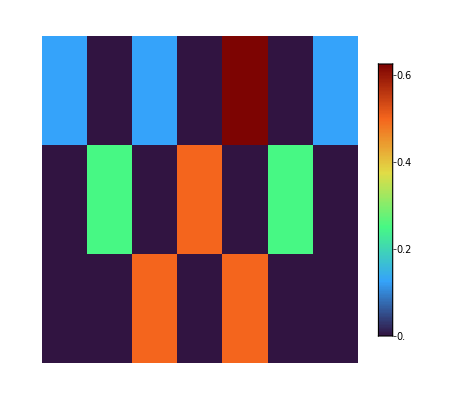

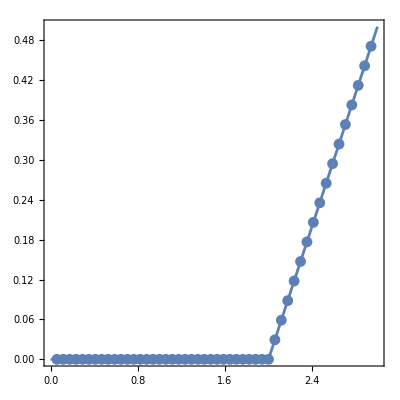

```mathematica
psi0={a,b};t=3;m=1;n=0;
probDistTimeL1=ProbDisTime[psi0,t,m,n];
PlotPosProbDisTime@probDistTimeL1[[2;;]]
expvalL1=ExpecValue[probDistTimeL1,t];
plotL1=PlotExpecValue[expvalL1]
```

```mathematica
probDistTimeL1
```

{{0,0,0,1.,0,0,0},{0,0,0.5,0,0.5,0,0},{0,0.25,0,0.5,0,0.25,0},{0.125,0,0.125,0,0.625,0,0.125}}

#### Estrategia 2

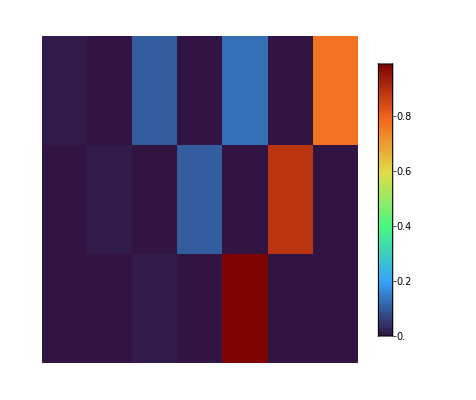

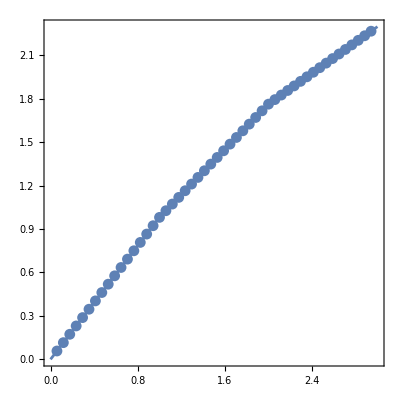

```mathematica
psi0={a,b};t=3;m=0;n=1;
probDistTimeL2=ProbDisTime[psi0,t,m,n];
PlotPosProbDisTime@probDistTimeL2[[2;;]]
expvalL2=ExpecValue[probDistTimeL2,t];
plotL2=PlotExpecValue[expvalL2]
```

```mathematica
probDistTimeL2
```

{{0,0,0,1.,0,0,0},{0,0,0.00960736,0,0.990393,0,0},{0,0.00945532,0,0.0996268,0,0.890918,0},{0.0091328,0,0.0996018,0,0.124216,0,0.767049}}

#### Estrategia 3

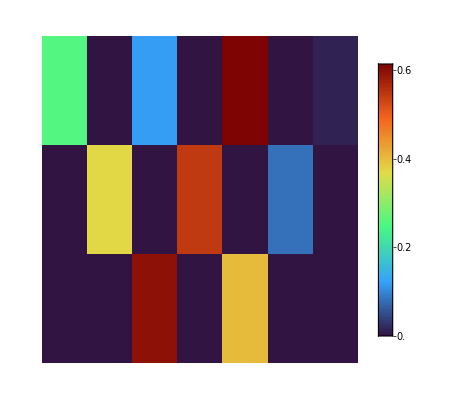

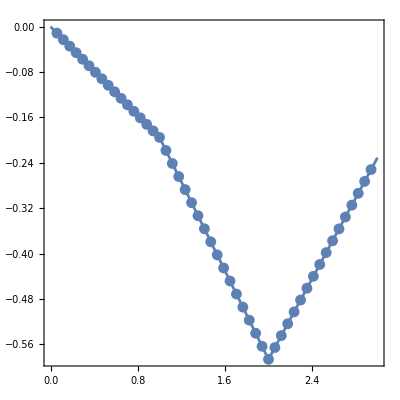

```mathematica
psi0={a,b};t=3;m=1;n=1;
probDistTimeL3=ProbDisTime[psi0,t,m,n];
PlotPosProbDisTime@probDistTimeL3[[2;;]]
expvalL3=ExpecValue[probDistTimeL3,t];
plotL3=PlotExpecValue[expvalL3]
```

```mathematica
probDistTimeL3
```

{{0,0,0,1.,0,0,0},{0,0,0.597545,0,0.402455,0,0},{0,0.373346,0,0.546399,0,0.0802554,0},{0.254439,0,0.118942,0,0.614258,0,0.0123607}}

#### Estrategia 4

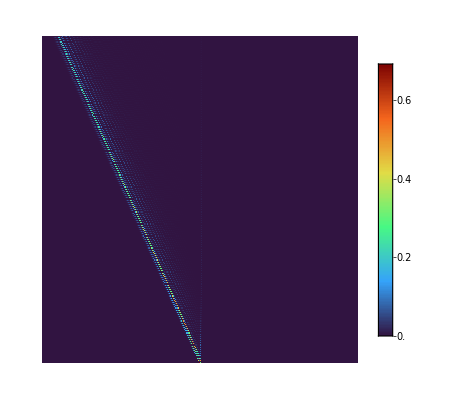

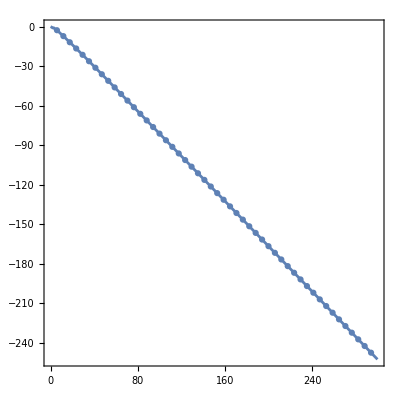

```mathematica
psi0={a,b};t=300;m=1;n=2;
probDistTimeL4=ProbDisTime[psi0,t,m,n];
PlotPosProbDisTime@probDistTimeL4[[2;;]]
expvalL4=ExpecValue[probDistTimeL4,t];
plotL4=PlotExpecValue[expvalL4]
```

#### Todas las estrategias perdedoras del artículo

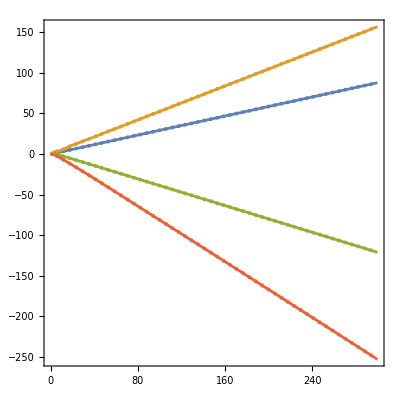

```mathematica
PlotExpecValue[{expvalL1,expvalL2,expvalL3,expvalL4},PlotLegends->{"","","",""}]
```

### Winning strategies

#### Estrategia 1

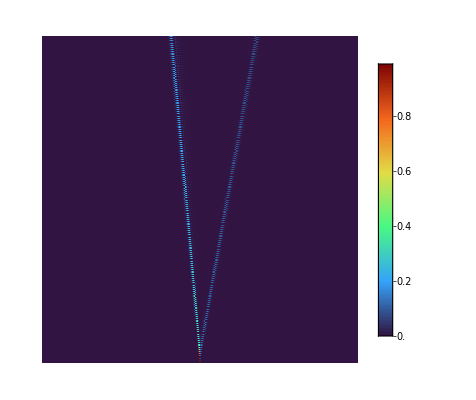

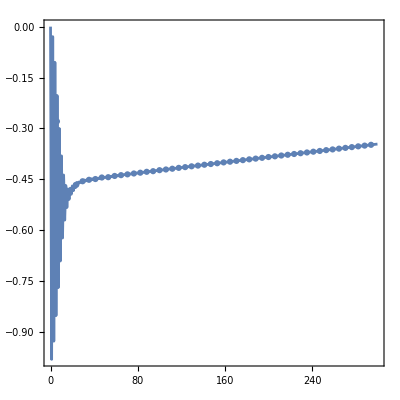

```mathematica
psi0={a,b};t=3;m=2;n=1;
probDistTimeW1=ProbDisTime[psi0,t,m,n];
PlotPosProbDisTime@probDistTimeW1[[2;;]]
expvalW1=ExpecValue[probDistTimeW1,t];
plotW1=PlotExpecValue[expvalW1]
```

#### Estrategia 2

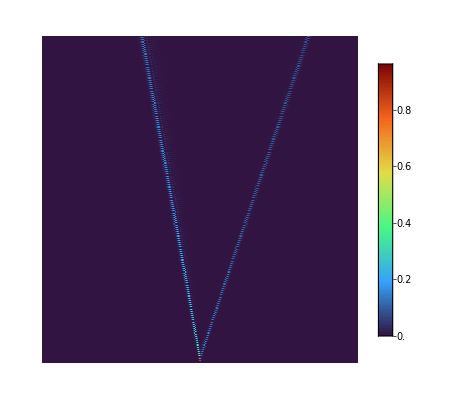

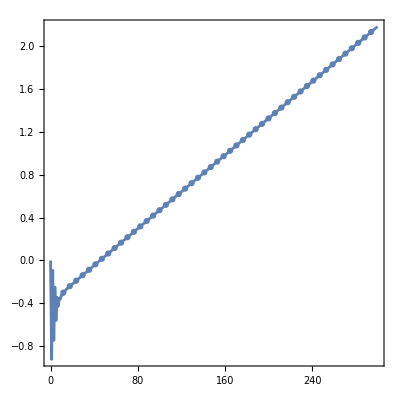

```mathematica
psi0={a,b};t=300;m=2;n=2;
probDistTimeW2=ProbDisTime[psi0,t,m,n];
PlotPosProbDisTime@probDistTimeW2[[2;;]]
expvalW2=ExpecValue[probDistTimeW2,t];
plotW2=PlotExpecValue[expvalW2]
```

#### Todas las estrategias ganadoras del artículo

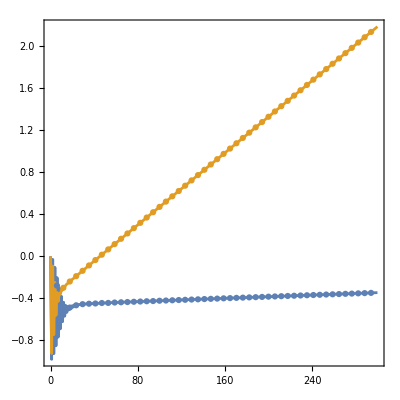

```mathematica
PlotExpecValue[{expvalW1,expvalW2},PlotLegends->{"",""}]
```

## Extras

### Valor de expectación

```mathematica
t=1000;
RepeatedTiming[List/@Range[-t,t];]
RepeatedTiming[{Range[-t,t]}ᵀ;]
```

{0.000136062,Null}

{4.00439×10^-6,Null}